```mathematica
M32x32=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Metropolis\\32x32\\experiment.txt","Table"];
M8x8x8=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Metropolis\\8x8x8\\experiment.txt","Table"];
M8x8x8x8=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Metropolis\\8x8x8x8\\experiment.txt","Table"];
```

```mathematica
WL32x32=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Wanglandau\\32x32\\experiment.txt","Table"];
WL8x8x8=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Wanglandau\\8x8x8\\experiment.txt","Table"];WL8x8x8x8=Import["E:\\Physics\\Projects\\Project2013A\\Results\\Data\\\
StateProfile\\Wanglandau\\8x8x8x8\\experiment.txt","Table"];
```

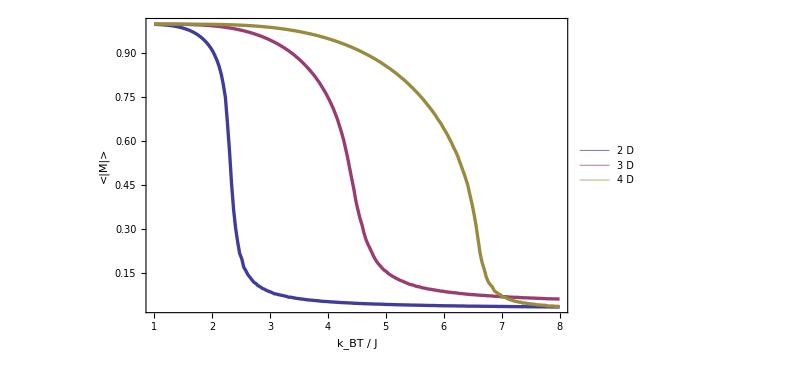

```mathematica
f1= magPlot[M32x32,M8x8x8,M8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\magnetization-metropolis.eps", f1];
```

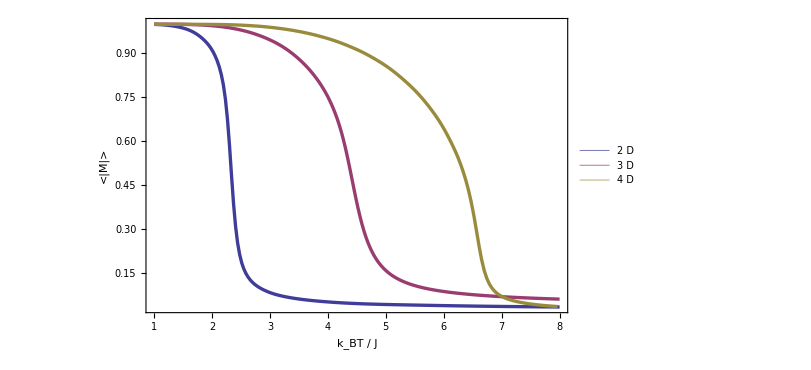

```mathematica
f2= magPlot[WL32x32,WL8x8x8,WL8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\magnetization-wanglandau.eps", f2];
```

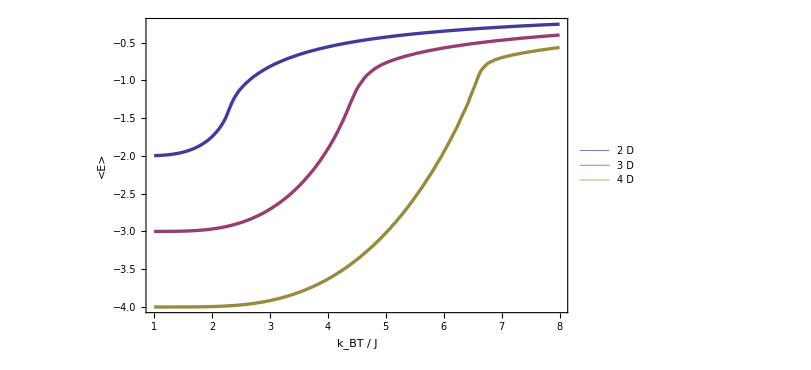

```mathematica
f3 = energyPlot[M32x32,M8x8x8,M8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\energy-metropolis.eps", f3];
```

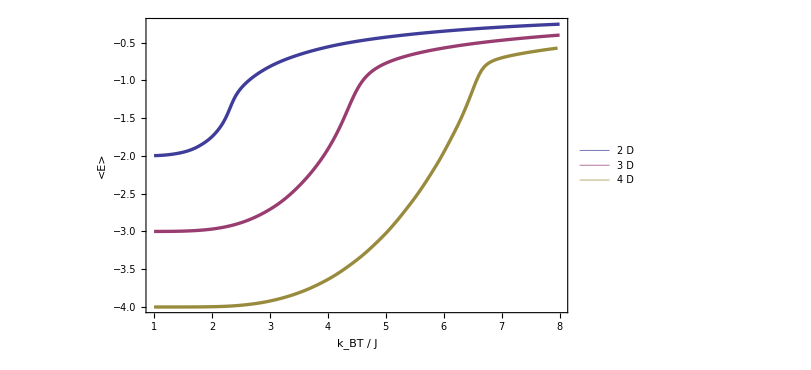

```mathematica
f4 =energyPlot[WL32x32,WL8x8x8,WL8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\energy-wanglandau.eps", f4];
```

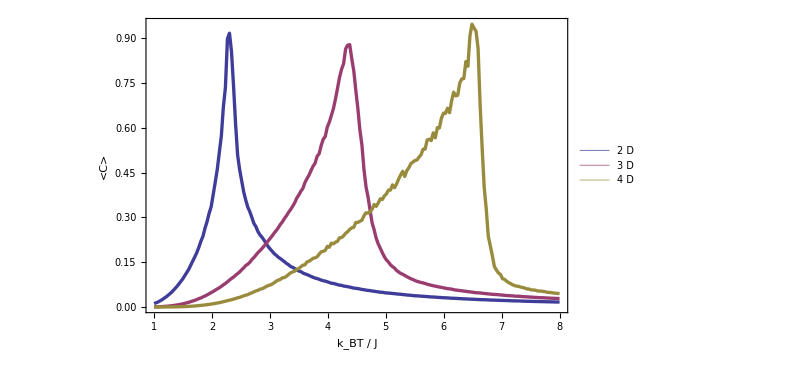

```mathematica
f5 =heatCapPlot[M32x32,M8x8x8,M8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\heatcapacity-metropolis.eps", f5];
```

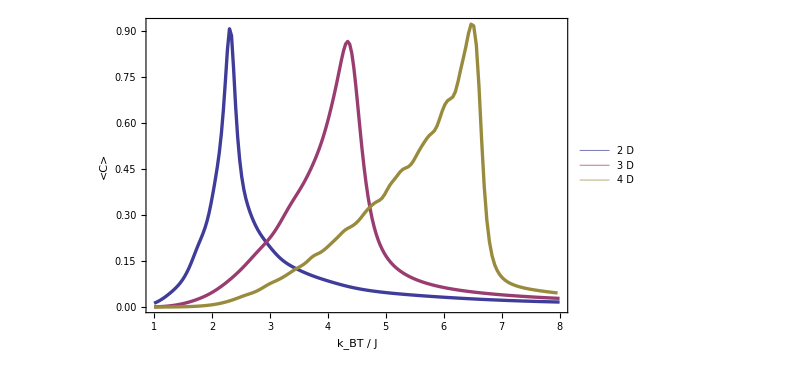

```mathematica
f6 = heatCapPlot[WL32x32,WL8x8x8,WL8x8x8x8, 2 D, 3D, 4 D] 
Export["E:\\Physics\\Projects\\Project2013A\\Results\\Write-up\\figures\\heatcapacity-wanglandau.eps", f6];
```